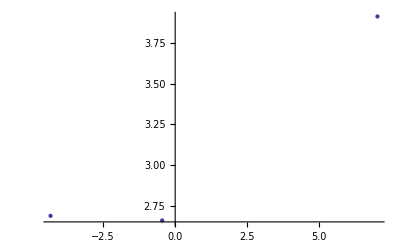

```mathematica
Clear all;
Clear[x];
n=3;
A=RandomReal[{-1,1},{n,n}];
b=RandomInteger[{-1,1},{n}];
xA=LinearSolve[A,b];
B=Transpose[A];
yB=LinearSolve[B,b];
xAyB=Table[{xA[[k]],yB[[k]]},{k,1,n}];
ListPlot[xAyB]
```